## Chapter 4 : Import and Export

```mathematica
Short[$ImportFormats,4](*Length[$ImportFormats] --> 256 formats*)
```

{3DS,7z,AC,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,ASC,ASE,AU,AVI,Base64,BDF,Binary,BioImageFormat,Bit,BLEND,BMP,«216»,WAV,Wave64,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XGL,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZSTD}

```mathematica
Import["/Users/macosx/Desktop/Hello_World.txt"]
```

Hello world!

```mathematica
Import["/Users/macosx/Desktop/Hello_World.txt","Text"]
```

Hello world!

## 4.1 Importing Files

### 4.1.1 CSV and TSV Files

```mathematica
Import["/Users/macosx/Desktop/Grocery_List.csv","CSV"]
```

{{id,grocery item,price,sold items,sales per day},{1,milk,4$,4,4 Jun 2019},{2,butter,3$,2,6 Jun 2019},{3,garlic,2$,1,7 Jun 2019},{4,apple,2$,4,1 Jun 2019},{5,orange,3$,5,8 Jun 2019},{6,orange juice,5$,2,8 Jun 2019},{7,cheese,5$,2,6 Jun 2019},{8,cookies,2$,5,9 Jun 2019},{9,grapes,4$,3,21 Jun 2019},{10,potato,2$,5,26 Jun 2019}}

```mathematica
Import["/Users/macosx/Desktop/Grocery_List.csv",{"Data",5;;10}]
```

{{4,apple,2$,4,1 Jun 2019},{5,orange,3$,5,8 Jun 2019},{6,orange juice,5$,2,8 Jun 2019},{7,cheese,5$,2,6 Jun 2019},{8,cookies,2$,5,9 Jun 2019},{9,grapes,4$,3,21 Jun 2019}}

```mathematica
Import["/Users/macosx/Desktop/Grocery_List.csv",{"Data",6,2}]
```

orange

```mathematica
Short[Import["/Users/macosx/Desktop/Color_table.tsv","TSV"]] (*Rest,to view the remain*)
```

{{number,color},{1,red},«7»,{9,magenta},{10,brown}}

```mathematica
Import["/Users/macosx/Desktop/Grocery_List.csv","CSV"];
Grid[%]
```

id | grocery item | price | sold items | sales per day
1 | milk | 4$ | 4 | 4 Jun 2019
2 | butter | 3$ | 2 | 6 Jun 2019
3 | garlic | 2$ | 1 | 7 Jun 2019
4 | apple | 2$ | 4 | 1 Jun 2019
5 | orange | 3$ | 5 | 8 Jun 2019
6 | orange juice | 5$ | 2 | 8 Jun 2019
7 | cheese | 5$ | 2 | 6 Jun 2019
8 | cookies | 2$ | 5 | 9 Jun 2019
9 | grapes | 4$ | 3 | 21 Jun 2019
10 | potato | 2$ | 5 | 26 Jun 2019

### 4.1.2 XLSX Files

```mathematica
path="/Users/macosx/Desktop/Grocery_List.xlsx";
Import[path,"Data"]
```

{{{id,grocery item, price, sold items,sales per day},{1.,milk,4$,4.,4-Jun-2019},{2.,butter,3$,2.,6-Jun-2020},{3.,garlic,2$,1.,7-Jun-2021},{4.,apple,2$,4.,1-Jun-2022},{5.,orange,3$,5.,8-Jun-2023},{6.,orange juice,5$,2.,8-Jun-2024},{7.,cheese,5$,2.,6-Jun-2025},{8.,cookies,2$,5.,9-Jun-2026},{9.,grapes,4$,3.,21-Jun-2027},{10.,potatoe,2$,5.,26-Jun-2028}}}

```mathematica
Import[path,#]&/@{"SheetCount","Sheets"}
```

{1,{Grocery_List}}

```mathematica
TableView[Import[path,{"Data",1},CharacterEncoding->"UTF-8"]]
```

idgrocery item price sold itemssales per day1.milk4$4.4-Jun-20192.butter3$2.6-Jun-20203.garlic2$1.7-Jun-20214.apple2$4.1-Jun-20225.orange3$5.8-Jun-20236.orange juice5$2.8-Jun-20247.cheese5$2.6-Jun-20258.cookies2$5.9-Jun-20269.grapes4$3.21-Jun-202710.potatoe2$5.26-Jun-2028

```mathematica
file="/Users/macosx/Desktop/Grocery_List_2.xlsx";Import[file,{"Dataset",1},HeaderLines->1]
```

```mathematica
Import[file,{"Dataset",1},"EmptyField"->"NaN",HeaderLines->1]
```

### 4.1.3 JSON Files

```mathematica
json=Import["/Users/macosx/Desktop/Sports_cars.json","JSON"]
```

{{Model→Enzo Ferrari,Year→2002,Cylinders→12,Horsepower HP→660,Weight Kg→1255},{Model→Koenigsegg CCX,Year→2000,Cylinders→8,Horsepower HP→806,Weight Kg→1180},{Model→Pagani Zonda,Year→2002,Cylinders→12,Horsepower HP→558,Weight Kg→1250},{Model→McLaren Senna,Year→2019,Cylinders→8,Horsepower HP→800,Weight Kg→1309},{Model→McLaren 675 LT,Year→2015,Cylinders→8,Horsepower HP→675,Weight Kg→1230},{Model→Bugatti Veyron,Year→2006,Cylinders→16,Horsepower HP→1001,Weight Kg→1881},{Model→Audi R8 Spyder ,Year→2010,Cylinders→10,Horsepower HP→525,Weight Kg→1795},{Model→Aston Martin Vantage,Year→2009,Cylinders→8,Horsepower HP→926,Weight Kg→1705},{Model→Maserati Gran Turismo,Year→2010,Cylinders→8,Horsepower HP→405,Weight Kg→1955},{Model→Lamborghini Aventador S,Year→2017,Cylinders→12,Horsepower HP→740,Weight Kg→1740}}

```mathematica
Map[Association,json,1]
```

{<|Model→Enzo Ferrari,Year→2002,Cylinders→12,Horsepower HP→660,Weight Kg→1255|>,<|Model→Koenigsegg CCX,Year→2000,Cylinders→8,Horsepower HP→806,Weight Kg→1180|>,<|Model→Pagani Zonda,Year→2002,Cylinders→12,Horsepower HP→558,Weight Kg→1250|>,<|Model→McLaren Senna,Year→2019,Cylinders→8,Horsepower HP→800,Weight Kg→1309|>,<|Model→McLaren 675 LT,Year→2015,Cylinders→8,Horsepower HP→675,Weight Kg→1230|>,<|Model→Bugatti Veyron,Year→2006,Cylinders→16,Horsepower HP→1001,Weight Kg→1881|>,<|Model→Audi R8 Spyder ,Year→2010,Cylinders→10,Horsepower HP→525,Weight Kg→1795|>,<|Model→Aston Martin Vantage,Year→2009,Cylinders→8,Horsepower HP→926,Weight Kg→1705|>,<|Model→Maserati Gran Turismo,Year→2010,Cylinders→8,Horsepower HP→405,Weight Kg→1955|>,<|Model→Lamborghini Aventador S,Year→2017,Cylinders→12,Horsepower HP→740,Weight Kg→1740|>}

```mathematica
Dataset[%]
```

```mathematica
Import["/Users/macosx/Desktop/Sports_cars.json","RawJSON"]
```

{<|Model→Enzo Ferrari,Year→2002,Cylinders→12,Horsepower HP→660,Weight Kg→1255|>,<|Model→Koenigsegg CCX,Year→2000,Cylinders→8,Horsepower HP→806,Weight Kg→1180|>,<|Model→Pagani Zonda,Year→2002,Cylinders→12,Horsepower HP→558,Weight Kg→1250|>,<|Model→McLaren Senna,Year→2019,Cylinders→8,Horsepower HP→800,Weight Kg→1309|>,<|Model→McLaren 675 LT,Year→2015,Cylinders→8,Horsepower HP→675,Weight Kg→1230|>,<|Model→Bugatti Veyron,Year→2006,Cylinders→16,Horsepower HP→1001,Weight Kg→1881|>,<|Model→Audi R8 Spyder ,Year→2010,Cylinders→10,Horsepower HP→525,Weight Kg→1795|>,<|Model→Aston Martin Vantage,Year→2009,Cylinders→8,Horsepower HP→926,Weight Kg→1705|>,<|Model→Maserati Gran Turismo,Year→2010,Cylinders→8,Horsepower HP→405,Weight Kg→1955|>,<|Model→Lamborghini Aventador S,Year→2017,Cylinders→12,Horsepower HP→740,Weight Kg→1740|>}

```mathematica
cars=Dataset[%];
```

```mathematica
cars[SortBy[#Year&]];
```

### 4.1.4 Web Data

```mathematica
Short[Import["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt","HTML"]]
```

AC Antigua and Barbuda AE United A…men ZA Zambia ZI Zimbabwe ZZ Ocean

```mathematica
Short[Import["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt","CSV"]]
```

{{AC Antigua and Barbuda},«217»,{ZZ Ocean}}

```mathematica
URLRead["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt"]
```

HTTPResponse[…]

```mathematica
URLDownload["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt"]
```

File[/private/var/folders/zs/hxtbpjpd5xb0krb6581764xm0000gn/T/igra2-country-list-7773b783-7536-4853-a91d-a1a0bc19ac74.txt]

## 4.2 Semantic Import

```mathematica
sImprt=SemanticImport["/Users/macosx/Desktop/Grocery_List.csv"]
```

### 4.2.1 Quantities

```mathematica
Quantity[2,"USDollars"]
```

2 $

```mathematica
Quantity[2,"USDollars"]//Head
```

Quantity

77 min

```mathematica
{QuantityMagnitude[Quantity[77, "Minutes"]],Head[%]}
```

{77,Quantity}

```mathematica
QuantityUnit[Quantity[77, "Minutes"]]
```

Minutes

### 4.2.2 Datasets with Quantities

```mathematica
{Quantity[77, "Minutes"]-Quantity[77, "Minutes"],Quantity[77, "Minutes"]+Quantity[77, "Minutes"],Quantity[77, "Minutes"]*Quantity[77, "Minutes"],Quantity[77, "Minutes"]/Quantity[77, "Minutes"],Quantity[77, "Minutes"]*Quantity[3, "Meters"]}
```

{0 min,154 min,5929 min^2,1,231 m min}

```mathematica
sImprt[[All,"price"]]
```

```mathematica
Normal[%]
```

{4 $,3 $,2 $,2 $,3 $,5 $,5 $,2 $,4 $,2 $}

```mathematica
QuantityMagnitude[#]&[%]
```

{4,3,2,2,3,5,5,2,4,2}

```mathematica
sImprt[[All,{"id","sales per day"}]]
```

```mathematica
Normal[Values[%]]//InputForm
```

{{1, DateObject[{2019, 6, 4}, "Day"]}, 
 {2, DateObject[{2019, 6, 6}, "Day"]}, 
 {3, DateObject[{2019, 6, 7}, "Day"]}, 
 {4, DateObject[{2019, 6, 1}, "Day"]}, 
 {5, DateObject[{2019, 6, 8}, "Day"]}, 
 {6, DateObject[{2019, 6, 8}, "Day"]}, 
 {7, DateObject[{2019, 6, 6}, "Day"]}, 
 {8, DateObject[{2019, 6, 9}, "Day"]}, 
 {9, DateObject[{2019, 6, 21}, "Day"]}, 
 {10, DateObject[{2019, 6, 26}, "Day"]}}

```mathematica
Association[Apply[Rule,%,1]]//InputForm
```

<|1 -> DateObject[{2019, 6, 4}, "Day"], 
 2 -> DateObject[{2019, 6, 6}, "Day"], 
 3 -> DateObject[{2019, 6, 7}, "Day"], 
 4 -> DateObject[{2019, 6, 1}, "Day"], 
 5 -> DateObject[{2019, 6, 8}, "Day"], 
 6 -> DateObject[{2019, 6, 8}, "Day"], 
 7 -> DateObject[{2019, 6, 6}, "Day"], 
 8 -> DateObject[{2019, 6, 9}, "Day"], 
 9 -> DateObject[{2019, 6, 21}, "Day"], 
 10 -> DateObject[{2019, 6, 26}, "Day"]|>

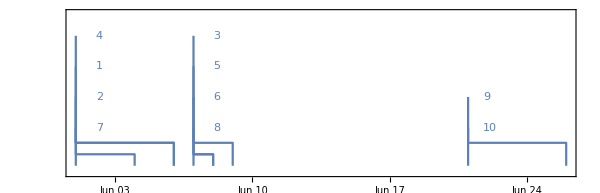

```mathematica
TimelinePlot[%]
```

### 4.2.3 Costume Imports (Dealing with Large Datasets)

```mathematica
SemanticImport["/Users/macosx/Desktop/Grocery_List.csv",{"Integer","String","Currency","Real","Date"}]
```

```mathematica
SemanticImport["/Users/macosx/Desktop/Grocery_List.csv",Automatic,"Rows"][[1;;5]]//InputForm
```

{{1, "milk", Quantity[4, "USDollars"], 4, DateObject[{2019, 6, 4}, 
   "Day"]}, {2, "butter", Quantity[3, "USDollars"], 2, 
  DateObject[{2019, 6, 6}, "Day"]}, 
 {3, "garlic", Quantity[2, "USDollars"], 1, DateObject[{2019, 6, 7}, 
   "Day"]}, {4, "apple", Quantity[2, "USDollars"], 4, 
  DateObject[{2019, 6, 1}, "Day"]}, 
 {5, "orange", Quantity[3, "USDollars"], 5, DateObject[{2019, 6, 8}, 
   "Day"]}}

```mathematica
SemanticImport["/Users/macosx/Desktop/Grocery_List.csv",Automatic,"Columns"][[1;;2]]
```

{{1,2,3,4,5,6,7,8,9,10},{milk,butter,garlic,apple,orange,orange juice,cheese,cookies,grapes,potato}}

```mathematica
SemanticImport["/Users/macosx/Desktop/Grocery_List.csv",ExcludedLines->{{10},{11}}]
```

```mathematica
SemanticImport["ExampleData/buildings.dat",<|"Name"->Automatic,"City"->Automatic,"Country"->Automatic,"Year"->Automatic|>,HeaderLines->1];
Select[%,#[[4]]<=2000&][[1;;10]]
```

## 4.3 Export

```mathematica
Short[$ExportFormats,5]
```

{3DS,AC,ACO,AIFF,ASE,AU,AVI,Base64,Binary,Bit,BLEND,BMP,BREP,BSON,Byte,BYU,BZIP2,C,CDF,«167»,WDX,WebP,WL,WLNet,WMLF,WXF,X3D,XBM,XGL,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP,ZPR,ZSTD}

```mathematica
Directory[]
```

/Users/macosx

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/macosx/Desktop

```mathematica
mydata=Table[Prime[i],{i,1,10}];
{Export["New_File.txt",mydata,"Table"],Export["New_File.csv",mydata]}
```

{New_File.txt,New_File.csv}

```mathematica
Export["/Users/macosx/Desktop/New_File.TSV",mydata,"TSV"]
```

/Users/macosx/Desktop/New_File.TSV

```mathematica
SystemOpen["/Users/macosx/Desktop/New_File.TSV"]
```

```mathematica
SystemOpen[NotebookDirectory[]]
```

```mathematica
tabD1=Table[i,{i,4}];
tabD2=SetPrecision[Table[i/11,{i,4}],3];
```

```mathematica
Export["Tabular_data.xls",{{tabD1},{tabD2}}]
```

Tabular_data.xls

```mathematica
Export["Tabular_data_2.xls",{"Page number 1"->tabD1,"Page number 2"->tabD2}]
```

Tabular_data_2.xls

```mathematica
Export["New_data.xls",Transpose[{tabD1,tabD2}]]
```

New_data.xls

```mathematica
Grid[Transpose[{tabD1,tabD2}]]
```

1 | 0.0909
2 | 0.182
3 | 0.273
4 | 0.364

```mathematica
table1={{"Dog","Wolf"},{"Cat","Leopard"},{"Pigeon","Shark"}};
Export["Animal_table.xls",table1]
```

Animal_table.xls

### 4.3.1 Other Formats

```mathematica
newD=Table[{i+j,i*j},{i,1,5},{j,1,5}];
{Export["File_text.txt",newD,"Text"],Export["File_dat.dat",newD,"Table"]}
```

{File_text.txt,File_dat.dat}

```mathematica
Export["File_text.txt",newD,"TSV"]
```

File_text.txt

```mathematica
{Export["File_csv.csv",newD,"CSV"],Export["File_tsv.tsv",newD,"TSV"]}
```

{File_csv.csv,File_tsv.tsv}

```mathematica
Export["File_csv.csv",newD,"CSV",TableHeadings->{"column 1","column 2","column 3","column 4","column 5"}]
```

File_csv.csv

```mathematica
labels={"Coordinates 1","Coordinates 2","Coordindates 3","Coordinates 4","Coordindates 5"};Export["File_csv.csv",newD,"CSV",TableHeadings->labels]
```

File_csv.csv

```mathematica
spData=ExampleData[{"Statistics","CarStoppingDistances"}]
```

{{4,2},{4,10},{7,4},{7,22},{8,16},{9,10},{10,18},{10,26},{10,34},{11,17},{11,28},{12,14},{12,20},{12,24},{12,28},{13,26},{13,34},{13,34},{13,46},{14,26},{14,36},{14,60},{14,80},{15,20},{15,26},{15,54},{16,32},{16,40},{17,32},{17,40},{17,50},{18,42},{18,56},{18,76},{18,84},{19,36},{19,46},{19,68},{20,32},{20,48},{20,52},{20,56},{20,64},{22,66},{23,54},{24,70},{24,92},{24,93},{24,120},{25,85}}

```mathematica
ExampleData[{"Statistics","CarStoppingDistances"},#]&/@{"Description","ColumnDescriptions"}
```

{Car stopping distances as a function of speed.,{Speed in miles per hour.,Stopping distance in feet.}}

```mathematica
spDataset=Dataset[spData,Background->LightBlue][All,<|#1->1,#2->2|>]&["Speed in miles per hours","Stopping distance in feet"]
```

```mathematica
Export["Dataset_csv.csv",spDataset,"CSV"]
```

Dataset_csv.csv

```mathematica
Export["Dataset_tsv.tsv",spDataset,"TSV"]
```

Dataset_tsv.tsv

### 4.3.2 XLS and XLSX Formats

```mathematica
Values@Normal@spDataset
```

{{4,2},{4,10},{7,4},{7,22},{8,16},{9,10},{10,18},{10,26},{10,34},{11,17},{11,28},{12,14},{12,20},{12,24},{12,28},{13,26},{13,34},{13,34},{13,46},{14,26},{14,36},{14,60},{14,80},{15,20},{15,26},{15,54},{16,32},{16,40},{17,32},{17,40},{17,50},{18,42},{18,56},{18,76},{18,84},{19,36},{19,46},{19,68},{20,32},{20,48},{20,52},{20,56},{20,64},{22,66},{23,54},{24,70},{24,92},{24,93},{24,120},{25,85}}

```mathematica
colTitles={"Speed in miles per hours","Stopping distance in feet"};
```

```mathematica
Short[exprtData=Prepend[%%,colTitles],1]
```

{{Speed in miles per hours,Stopping distance in feet},«49»,{25,85}}

```mathematica
Export["Stopping_distance_Dataset.xlsx",exprtData,"XLSX"]
```

Stopping_distance_Dataset.xlsx

### 4.3.3 JSON Format

```mathematica
Association@{"Name"->"Ellis","Date of birth"->"1990,01,04","Height"->"180 cm","Favorite color"->"Red","Hobbies"->"Soccer, Pc gaming, Board games","Social netwoks"->"Twitter, Facebook"};
Export["File_json.json",%,"JSON"]
```

File_json.json

```mathematica
Association@{"Name"->"Ellis","Date of birth"->DateObject[{1990,01,04}],"Height"->Quantity[180,"Centimeters"],"Favorite color"->"Red","Hobbies"->"Soccer, Pc gaming, Board games","Social netwoks"->"Twitter, Facebook"};
user=Dataset[%]
```

```mathematica
Export["Dataset_json.json",user,"JSON"]
```

Dataset_json.json

```mathematica
assoc1=<|"Log in Date"->DateObject[{2020,06,29}],"User ID"->123,"Status"->"Active"|>;
assoc2=<|"Log in Date"->DateObject[{2020,06,28}],"User ID"->122,"Status"->"Not Active"|>;Dataset[{assoc1,assoc2}] 
Export["Dataset2_json.json",%,"JSON"]
```

Dataset2_json.json

```mathematica
assoc3="Player A"->Association["Date"->DateObject[{2020,06,29}],"User ID"->123,"Status"->"Active"];assoc4="Player B"->Association["Date"->DateObject[{2020,06,28}],"User ID"->122,"Status"->"Not Active"];Dataset[{<|assoc3,assoc4|>}]
```

```mathematica
Export["Dataset3_json.json",%,"JSON"]
```

Dataset3_json.json

```mathematica
rules={"apple"->3,"car"->"3","2"->2};
Export["Rules.json",rules,"JSON"]
```

Rules.json

```mathematica
arry=Array[{#1,#2}&,{4,4}]
Export["Array.json",arry,"JSON"]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}},{{4,1},{4,2},{4,3},{4,4}}}

Array.json

### 4.3.4 Content File Objects

```mathematica
Association@{"Name"->"Ellis","Date of birth"->DateObject[{1990,01,04}],"Height"->Quantity[180,"Centimeters"],"Favorite color"->"Red","Hobbies"->"Soccer, Pc gaming, Board games","Social netwoks"->"Twitter, Facebook"};
user=Dataset[%];
jsonFile=Export["Dataset_json_2.json",user,"JSON"];
```

```mathematica
AbsoluteFileName[jsonFile]
```

/Users/macosx/Desktop/Dataset_json_2.json

```mathematica
ContentObject[%]
```

ContentObject[…]

```mathematica
ContentObject[%%]["Properties"]
```

{CreationDate,Plaintext}

### 4.3.5 Searching Files with Wolfram Language

```mathematica
NotebookDirectory[]
```

/Users/macosx/Desktop/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/macosx/Desktop

```mathematica
FileNames[]
```

```mathematica
FindFile["Color_table.txt"]
```

/Users/macosx/Desktop/Color_table.txt

```mathematica
FileNames["*.txt"]
```

{Color_table.txt,File_text.txt,Hello_World.txt,New_File.txt}

## 4.4 Connecting to External Services

### 4.4.1 External Connections

```mathematica
FindExternalEvaluators["Shell"]//Normal//Print
```

<|e62f301a-113c-2233-787d-bbc45334624d→<|System→Shell,Evaluator→/bin/bash,Executable→/bin/bash,Target→/bin/bash,Registered→False|>,9bcd31a2-7c42-bbd1-9dc1-4835a345f5e7→<|System→Shell,Evaluator→/bin/sh,Executable→/bin/sh,Target→/bin/sh,Registered→False|>,e2eccf19-48e9-c8bf-e536-84acda0d1700→<|System→Shell,Evaluator→/bin/zsh,Executable→/bin/zsh,Target→/bin/zsh,Registered→False|>|>

echo 'Hello World!'

Hello World!

Success[…]

### 4.4.2 External Resources

```mathematica
RegisterExternalEvaluator["NodeJS","/opt/homebrew/bin/node"]
```

629ba62a-8d17-e9fe-6cd9-870f94c7933c

```mathematica
FindExternalEvaluators["NodeJS"]//Normal//Print
```

<|629ba62a-8d17-e9fe-6cd9-870f94c7933c→<|System→NodeJS,Version→21.2.0,Target:>/opt/homebrew/bin/node,Executable:>/opt/homebrew/bin/node,Registered→True|>|>

```mathematica
ExternalEvaluate["NodeJS","Math.sqrt(25)"]
```

5

```mathematica
jsFun1 =ExternalFunction["NodeJS","Math.sqrt"]
```

ExternalFunction[…]

```mathematica
jsFun1[#]&/@{25,36,49,64}
```

{5,6,7,8}

```mathematica
jsFun2=
ExternalFunction["NodeJS","(number) => Math.sqrt(number);"];
jsFun2[#]&/@{25,36,49,64}
```

{5,6,7,8}

(num1, num2) => {
  var sum = num1 + num2;
  return Math.sqrt(sum);
}

ExternalFunction[…]

```mathematica
%[18,18]
```

6

```mathematica
UnregisterExternalEvaluator["NodeJS","/opt/homebrew/bin/node"]
```

629ba62a-8d17-e9fe-6cd9-870f94c7933c

### 4.4.3 Database and File Operations (SQL)

```mathematica
DatabaseReference[FindFile["ExampleData/ecommerce-database.sqlite"]];
Shallow[%]
```

DatabaseReference[<|Backend→SQLite,Name→/Applications/Mathematica.app/Contents/Documentation/English/System/ExampleData/ecommerce-database.sqlite|>]

SELECT name FROM sqlite_master WHERE type='table'

SELECT * FROM offices;

SELECT territory, city FROM offices ORDER BY territory;